```mathematica
$Path=Join[$Path,{"~/Documents/Sparse\ Grids/Summary/"}];
Import["Methods\ and\ Functions\ for\ d-D\ Grids.m"]
```

# Summary of Work so Far

## As of June 27

### Basis in 1-D

We use ‘hat’-like functions, which are translates and scalings of

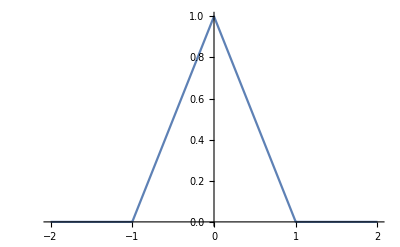

```mathematica
Plot[ϕ[x],{x,-2,2}]
```

We will always be working on the unit interval [0,1]. One way to interpolate a function is to use a Lagrange basis. We rescale all the hat functions down by a factor of 2^n and associate one with each point from 0 to 1 in increments of 2^-n for a total of 2^n+1.

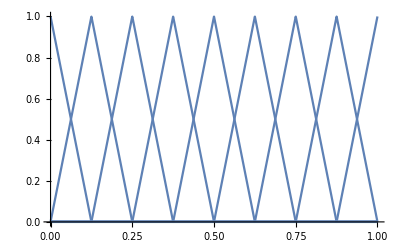

```mathematica
Plot[Table[ψ[3,i][x],{i,0,8}],{x,0,1},PlotRange->Full]
```

We can then express a function in terms of this basis as:

{0,Sin[π/8],1/(√2),Cos[π/8],1,Cos[π/8],1/(√2),Sin[π/8],0}

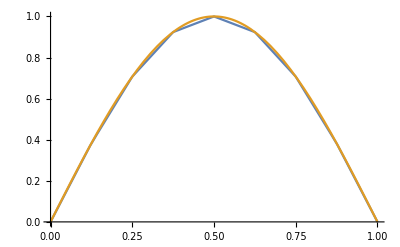

```mathematica
standardCoeffs=standardCoefficients[Sin[Pi #⟦1⟧]&,{3}]
Plot[{standardReconstruct[standardCoeffs,{3},{x}],Sin[Pi x]},{x,0,1}]
```

The basis that we will use more often is called the Hierarchical basis. It is this basis that allows us to work with sparse grids. Instead of having all the hat functions have the same width, there is a hierarchy of functions at various resolutions. The benefit is that increasing the resolution does not mean that we need to change all 2^n basis functions in 1-D to 2^(n+1), but instead we only need to add 2^nnew ones, keeping the ones we already have.

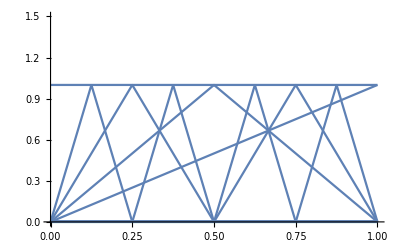

```mathematica
Plot[Table[Table[ϕ[l,i][x],{i,1,switch[2l+1]}],{l,-1,3}],{x,0,1},PlotRange->{0,1.5}]
```

The coefficients are only slightly more involved to get, but the final reconstruction is identical.

```mathematica
fullCoeffs=fullCoefficients[Sin[Pi #⟦1⟧]&,{3}]
Plot[{fullReconstruct[fullCoeffs,{x},{3}],Sin[Pi x]},{x,0,1}]
```

SparseArray[<7>, {5, 4}]

-Graphics-

### Hierarchical Basis 2-D

By taking tensor products of hat functions, we can obtain a basis for higher dimensions, like for example 2-D:

```mathematica
Plot3D[ϕ[{1,2},{1,2}][{x,y}],{x,0,1},{y,0,1}]
```

-Graphics3D-

### Sparse Basis 2-D